# Data Based Stability Analysis

## For unidirectional tipping system

## Functions & Initializations

Functions need descriptions

```mathematica
StochTippingDataGen[A_,SpecificGraph_,d_,TippedNodes_,rm_,DriverNodes_,UValue_,Noise_,dt_,InitVal_,FinalTime_]:=(Module[{n,B,r,eq,GenData,a=-1,b=1,x0=0},

n=Length[A];
r= Table[0&,n];

t=.;

r[[TippedNodes]]=rm;
B=A;
Do[B[[i,Complement[VertexOutComponent[SpecificGraph,i,1],{i}]]]=UValue,{i,DriverNodes}];



eq=Table[ⅆSymbol["x"<>ToString[i]][t]==(r[[i]][t]+b*(Symbol["x"<>ToString[i]][t]-x0)+a*(Symbol["x"<>ToString[i]][t]-x0)^3+d*Sum[Sqrt[-b/a]*Transpose[A][[i,j]],{j,1,n,1}]+d*Sum[Transpose[B][[i,j]]*(Symbol["x"<>ToString[j]][t]-x0),{j,1,n,1}])ⅆt+Noise*ⅆSymbol["w"<>ToString[i]][t],{i,1,n,1}];



GenData=RandomFunction[ItoProcess[eq,Table[Symbol["x"<>ToString[k]][t],{k,1,n}],{Table[Symbol["x"<>ToString[k]],{k,1,n}],InitVal},t,Table[Symbol["w"<>ToString[k]]\[Distributed]WienerProcess[],{k,1,n}]],{0.,FinalTime,dt},Method->"KloedenPlatenSchurz"];

GenData=TemporalData[Table[GenData["Values"][[;;,l]],{l,1,n}],{0,FinalTime}];

GenData
]
)
(*this func is constructed for a=-1 and b=1 and x0=0.5 but we can probably change them
but same values for all nodes for now*)
(*We have the same problem of global variables x1, x2, ..*)
(*remember to check the equation for a=-1 and compute r from Rs*)
```

```mathematica
Clear[MakeWindow];
MakeWindow[Data_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO,TP},
TP=Length[Data];
WO=(1-Overlap)*WL;
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
(*{Lb,Hb}*)
Data[[Lb;;Hb]]
]
```

```mathematica
Window[TP_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO},
(*TP=Length[Data];*)
WO=(1-Overlap)*WL;
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
{Lb,Hb}

]
```

```mathematica
TippingCoefsBasic[TimeSerieValues_,i_,dt_]:=(Module[{Y,Mat,Dim,TP,MatrixRowDef,MatrixRow,Coefs,CoefKeys},
Dim=Dimensions[Values[TimeSerieValues]];
TP=Dim[[2]];



CoefKeys=Join[{"\*SubscriptBox[R, "<>StringDelete[ToString[i]," "]<>"]"},Table["\*SubscriptBox[x, "<>StringDelete[ToString[j]," "]<>"]",{j,Keys[TimeSerieValues]}],{"\*SubscriptBox[x, "<>StringDelete[ToString[i]," "]<>"]"<>"^3"}];

MatrixRowDef=Join[{Table[1,TP]},Values[TimeSerieValues]];

MatrixRow=Join[MatrixRowDef,{TimeSerieValues[i]^3}];

Mat=Join[Table[MatrixRow.MatrixRowDef[[k]]/TP,{k,1,Dim[[1]]+1}],{MatrixRow.TimeSerieValues[i]^2/TP}];

Y=Join[Table[(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).MatrixRowDef[[k]][[;;-2]]/(TP-1),{k,1,Dim[[1]]+1}],{(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).TimeSerieValues[i][[;;-2]]^2/(TP-1)}];

Coefs=Association[Table[CoefKeys[[h]]->(LinearSolve[Mat,Y]/dt)[[h]],{h,1,Dim[[1]]+2}]];

Dataset[Coefs]
]
)
```

```mathematica
TippingCoefsWithWindow[TimeSerieValues_,i_,l_,dt_,WL_,Overlap_]:=(Module[{WindowTimeSerieValues,WindowTimeSerieValuesShuffle,Coefs,Errors,CoefsAfterError},

WindowTimeSerieValues=(MakeWindow[#,WL,Overlap,l]&)/@TimeSerieValues;

Coefs=TippingCoefsBasic[WindowTimeSerieValues,i,dt];

Coefs
]
)
```

```mathematica
NFixedPointsAndEigenValuesComplete[FixedPointEquations_,JacobianEquations_,n_]:=(Module[{FixedPoints,FixedPointsRules,EigenValues,StableFixedPointIndicies,UnStableFixedPointIndicies},
(**)

FixedPointsRules=NSolve[FixedPointEquations,Table[Indexed[x,i],{i,1,n}],Reals];
FixedPoints=Table[Indexed[x,i],{i,1,n}]/.FixedPointsRules;
EigenValues=Map[Eigenvalues][JacobianEquations/.FixedPointsRules];
StableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[And,Map[(#<0&),#],{0}]&),1];
UnStableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[Or,Map[(#≥0&),#],{0}]&),1];
{{Length[FixedPoints],EigenValues,FixedPoints},{Length[Extract[FixedPoints,StableFixedPointIndicies]],Extract[EigenValues,StableFixedPointIndicies],Extract[FixedPoints,StableFixedPointIndicies]},{Length[Extract[FixedPoints,UnStableFixedPointIndicies]],Extract[EigenValues,UnStableFixedPointIndicies],Extract[FixedPoints,UnStableFixedPointIndicies]}}

]
)(*This is changed to get n*)
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\texlive\\2017\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.1\\bin\\gswin64c.exe"
];
```

## Data Generation

### Network

```mathematica
graph=Graph[{0->1,1->2,3->2,4->2,4->5,4->6,6->7,7->8,4->9,0->3,0->7,1->4,2->8,3->1,4->0,7->5,9->3}/.{0->1,1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10},VertexLabels->Automatic];
A=AdjacencyMatrix[graph]//Normal;
```

### r_{1} Sigmoid Function

```mathematica
rSigmoid[t_]:=0.79(1-(1/(1+Exp[-t/100+25])))
```

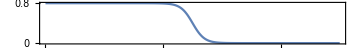

```mathematica
grsig=Plot[rSigmoid[t],{t,0,5000},Frame->True,
FrameTicks->{{{0.8,0},None},{{0,1000,2000,{2500,MaTeX["t_c",FontSize->10],0.12,Directive[Dashed,Orange]},3000,4000,5000},None}},FrameTicksStyle->Directive[FontFamily->"Times",12,Black],
ImageSize->Medium,
AspectRatio->1/8.5,
(*PlotLabel->Style["C",12,FontFamily->"Times"],*)
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["r_1",FontSize->12]}]
```

```mathematica
(*Export[NotebookDirectory[]<>"r_Sigmoid.pdf",grsig]*)
```

C:\Users\alish\Desktop\stability paper\r_Sigmoid.pdf

### Data

Noise = sqrt(0.5), dt = 0.005, Tf = 5000

```mathematica
SeedRandom[859];
Noise=Sqrt[0.5];(*Noise is larger than convergence tests*)
dt=0.005;
GenData=StochTippingDataGen[A,graph,0.3,{5},rSigmoid,{1},1,Noise,dt,Table[1.2,10],5000](*Tf if 5000*)
```

TemporalData[<<10>>]

```mathematica
GenData["Paths"][[1]]
```

```mathematica
Do[Export[NotebookDirectory[]<>"10D_x_"<>ToString[m]<>"_5000_0.005_0.5.txt",GenData["Paths"][[m]],"Table","FieldSeparators"->Tab],{m,1,10}]
```

```mathematica
TimeSerieValues=Association@Table[ToString[i]->GenData["ValueList"][[i]],{i,1,10}];
```

```mathematica
(*Mean/@GenData["ValueList"]*)
```

```mathematica
(*g1=ListPlot[GenData["Paths"][[1]][[;;;;1]],PlotRange->All,ImageSize->Large,AspectRatio->1/8.5,PlotLabel->Style["A",FontFamily->"Times",12],Axes->False,Frame->True,FrameTicks->{{{-1,1},None},{Table[i,{i,0,5000,1000}],None}},FrameTicksStyle->Directive[FontFamily->"Times",12],FrameLabel->{None,Style[,12]},PlotStyle->{Thickness[0.002],Black},Joined->True]*)
```

### Windowing

Window Size 500000, Overlap = 95%

```mathematica
WinSize=500000;
Overlap=95/100;
```

```mathematica
MN=With[{TP=1000000,Overlap=Overlap,WL=WinSize},(TP-(Overlap*WL))/((1-Overlap)*WL)]
```

21

## Coefficients

```mathematica
Coeffs=MapThread[List,Table[Table[Values@Normal[TippingCoefsWithWindow[TimeSerieValues,ToString[i],l,dt,WinSize,Overlap]],{l,1,MN}],{i,1,10}]];
```

## Data Based Stability Analysis

## Fixed Points & Eigen Values Computation

```mathematica
FixedPointEquationsWin=With[{n=10},Table[Table[Coeffs[[l,i]][[1]]+Sum[Coeffs[[l,i]][[j+1]]Indexed[x,j],{j,1,n}]+Coeffs[[l,i,n+2]]Indexed[x,i]^3==0,{i,1,n}],{l,1,MN}]];
```

```mathematica
JacobianEquationsWin=With[{n=10},Table[D[Table[Coeffs[[l,i]][[1]]+Sum[Coeffs[[l,i]][[j+1]]Indexed[x,j],{j,1,n}]+Coeffs[[l,i,n+2]]Indexed[x,i]^3,{i,1,n}],{Table[Indexed[x,i],{i,1,n,1}]}],{l,1,MN}]];
```

```mathematica
(*fr=NSolve[FixedPointEquations[[1]],Table[Indexed[x,i],{i,1,2}],Reals]*)
```

```mathematica
(*JacobianEquations[[1]]/.fr*)
```

```mathematica
(*With[{l=8},With[{DyData=(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l]},DyData[[2,3]]]]*)
```

```mathematica
{time,StableFixedPointsOneWindows}=Timing@Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],10])&[l][[2,3]],{l,1,1}];
time
StableFixedPointsOneWindows(*to check computation time 
and first fixed point*)
```

4.42188

```mathematica
StableFixedPointsWindows=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],10])&[l][[2,3]],{l,1,MN}];
```

$Aborted

```mathematica
StableFixedPointsEigensWindows=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],10])&[l][[2,2]],{l,1,MN}];
```

```mathematica
StableFixedPointsWindows[[;;,1]](*$$$$$$$$$$$$$*)
```

{{1.26719,1.23722},{1.26656,1.23809},{1.25927,1.23744},{1.25673,1.23664},{1.24884,1.23813},{1.23954,1.23972},{1.23382,1.2415},{1.22736,1.24042},{1.21858,1.24057},{1.20575,1.23734},{1.19083,1.23779},{1.17608,1.2366},{1.15348,1.23515},{1.13632,1.23205},{1.11242,1.22915},{1.09207,1.22843},{1.07096,1.2259},{1.03903,1.22452},{1.00494,1.22202},{0.977982,1.21887},{0.976392,1.21577}}

```mathematica
StableFixedPointsEigensWindows[[;;,1]]
```

{{-3.81166,-3.52153},{-3.82628,-3.53378},{-3.75403,-3.43402},{-3.71535,-3.40822},{-3.66246,-3.30361},{-3.65972,-3.1862},{-3.68723,-3.10288},{-3.66973,-3.01029},{-3.65877,-2.87353},{-3.65102,-2.66851},{-3.61791,-2.4891},{-3.59732,-2.29107},{-3.5816,-2.07328},{-3.51705,-1.99315},{-3.49256,-1.84572},{-3.56367,-1.80927},{-3.50368,-1.73416},{-3.46633,-1.55592},{-3.44253,-1.45298},{-3.39626,-1.4314},{-3.36206,-1.59007}}

```mathematica
LambdaMin=Min/@StableFixedPointsEigensWindows[[;;,1]];
```

```mathematica
LambdaMin={-6.12244,-6.11078,-6.1487,-6.18067,-6.16159,-6.11907,-6.14715,-6.13487,-6.14861,-6.14026,-6.08052,-6.09731,-6.13016,-6.13385,-6.17173,-6.15107,-6.20731,-6.26887,-6.22832,-6.21152,-6.228};
```

```mathematica
LambdaMax=Max/@StableFixedPointsEigensWindows[[;;,1]];
```

```mathematica
LambdaMax={-3.70809,-3.71312,-3.7244,-3.70336,-3.65495,-3.65166,-3.63815,-3.63755,-3.63831,-3.58852,-3.56152,-3.50573,-3.51075,-3.47374,-3.45751,-3.46783,-3.45203,-3.46582,-3.46535,-3.52161,-3.55814};
```

```mathematica
Export[NotebookDirectory[]<>"Eigenvalue_max_Data.txt",Transpose@LambdaMax]
```

C:\Users\alish\Desktop\stability paper\Eigenvalue_max_Data.txt

```mathematica
Export[NotebookDirectory[]<>"Eigenvalue_min_Data.txt",Transpose@LambdaMin]
```

C:\Users\alish\Desktop\stability paper\Eigenvalue_min_Data.txt

```mathematica
Ts=Table[(Plus@@(Window[WinSize,Overlap,l])-1)/2,{l,1,MN}]/1000000*5000
```

{1250,1375,1500,1625,1750,1875,2000,2125,2250,2375,2500,2625,2750,2875,3000,3125,3250,3375,3500,3625,3750}

## Figures

```mathematica
leglambda=PointLegend[{Black,Red},{MaTeX["\\lambda_{min}",FontSize->10],MaTeX["\\lambda_{max}",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

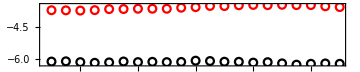

```mathematica
glambda=ListPlot[{MapThread[List,{Ts,(*1/Abs@*)LambdaMin}],MapThread[List,{Ts,(*1/Abs@*)LambdaMax}]},
Frame->True,
FrameTicks->{{(*Range[-3.5,-1.5,1]*)Automatic,None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,Automatic(*{-4,-1}*)},
PlotLegends->Placed[leglambda,{0.2,0.5}]]
```

```mathematica
Export[NotebookDirectory[]<>"2Eigenvalue_sqrt0.5_500.pdf",glambda]
```

C:\Users\alish\Desktop\stability paper\2Eigenvalue_sqrt0.5_500.pdf

```mathematica
legtime=PointLegend[{Black,Red},{MaTeX["1/|\\lambda_{min}|",FontSize->10],MaTeX["1/|\\lambda_{max}|",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

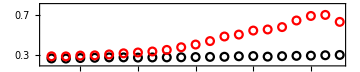

```mathematica
gtimescale=ListPlot[{MapThread[List,{Ts,1/Abs@LambdaMin}],MapThread[List,{Ts,1/Abs@LambdaMax}]},
Frame->True,
FrameTicks->{{Range[0.3,0.7,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{0.2,0.8}},
PlotLegends->Placed[legtime,{0.25,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2timescale_sqrt0.5_500.pdf",glambda]
```

C:\Users\alish\Desktop\stability paper\2timescale_sqrt0.5_500.pdf

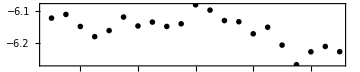

```mathematica
gmin=ListPlot[MapThread[List,{Ts,(*1/Abs@*)LambdaMin}],
Frame->True,
FrameTicks->{{(*Range[-3.8,-3.4,0.2]*)Automatic,None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{min}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,(*{-4,-3.2}*)Automatic}]
```

```mathematica
Export[NotebookDirectory[]<>"min_Eigenvalue_sqrt0.5_500.pdf",gmin]
```

C:\Users\alish\Desktop\stability paper\min_Eigenvalue_sqrt0.5_500.pdf

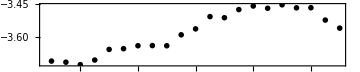

```mathematica
gmax=ListPlot[MapThread[List,{Ts,(*1/Abs@*)LambdaMax}],
Frame->True,
FrameTicks->{{(*Range[-3.5,-1.5,1]*)Automatic,None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{max}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,(*{-4,-1}*)Automatic}]
```

```mathematica
Export[NotebookDirectory[]<>"max_Eigenvalue_sqrt0.5_500.pdf",gmin]
```

C:\Users\alish\Desktop\stability paper\max_Eigenvalue_sqrt0.5_500.pdf

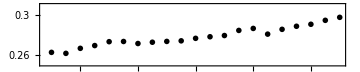

```mathematica
gtmin=ListPlot[MapThread[List,{Ts,1/Abs@LambdaMin}],
Frame->True,
FrameTicks->{{Range[0.26,0.30,0.02],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{min}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{0.25,0.31}}]
```

```mathematica
Export[NotebookDirectory[]<>"min_timescale_sqrt0.5_500.pdf",gtmin]
```

C:\Users\alish\Desktop\stability paper\min_timescale_sqrt0.5_500.pdf

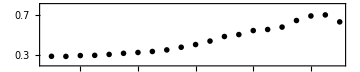

```mathematica
gtmax=ListPlot[MapThread[List,{Ts,1/Abs@LambdaMax}],
Frame->True,
FrameTicks->{{Range[0.3,0.7,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{max}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{0.2,0.8}}]
```

```mathematica
Export[NotebookDirectory[]<>"max_timescale_sqrt0.5_500.pdf",gtmax]
```

C:\Users\alish\Desktop\stability paper\max_timescale_sqrt0.5_500.pdf

## Figures and Data for Theory

```mathematica
graph=Graph[{0->1,1->2,3->2,4->2,4->5,4->6,6->7,7->8,4->9,0->3,0->7,1->4,2->8,3->1,4->0,7->5,9->3}/.{0->1,1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10},VertexLabels->Automatic];
A=AdjacencyMatrix[graph]//Normal;
```

```mathematica
AllrsFunc=Table[If[i==5,rSigmoid,0&],{i,1,10}](*node numbers and tipping node specification*)
```

{0&,0&,0&,0&,rSigmoid,0&,0&,0&,0&,0&}

```mathematica
TsTh={1250,1375,1500,1625,1750,1875,2000,2125,2250,2375,2500,2625,2750,2875,3000,3125,3250,3375,3500,3625,3750};
```

```mathematica
FixedPointEquationsWinTh=With[{n=10},Table[Table[AllrsFunc[[i]][t]+0.3Sum[A[[j,i]](Indexed[x,j]+1),{j,1,n}]-Indexed[x,i]^3+Indexed[x,i]==0,{i,1,n}],{t,TsTh}]];(*d=0.3, Tf(5000), nodes number(n)*)
```

```mathematica
JacobianEquationsWinTh=With[{n=10},Table[D[Table[AllrsFunc[[i]][t]+0.3Sum[A[[j,i]](Indexed[x,j]+1),{j,1,n}]-Indexed[x,i]^3+Indexed[x,i],{i,1,n}],{Table[Indexed[x,i],{i,1,n,1}]}],{t,TsTh}]];(*d=0.3, Tf(5000), nodes number(n)*)
```

```mathematica
(*With[{l=8},With[{DyData=(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l]},DyData[[2,3]]]]*)
```

```mathematica
StableFixedPointsWindowsTh=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWinTh[[#]],JacobianEquationsWinTh[[#]],2])&[l][[2,3]],{l,1,Length@TsTh}]
```

$Aborted

```mathematica
StableFixedPointsEigensWindowsTh=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWinTh[[#]],JacobianEquationsWinTh[[#]],2])&[l][[2,2]],{l,1,Length@TsTh}];
```

```mathematica
StableFixedPointsWindowsTh[[;;,1]](*$$$$$$$$$$$$$*)
```

{{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27301,1.24421},{1.27299,1.24421},{1.27283,1.2442},{1.27165,1.2441},{1.26322,1.2434},{1.21469,1.23939},{-0.869238,-0.979776},{-0.980712,-0.997094},{-0.997346,-0.999602},{-0.99964,-0.999946},{-0.999951,-0.999993},{-0.999993,-0.999999},{-0.999999,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.}}

```mathematica
StableFixedPointsEigensWindowsTh[[;;,1]]
```

{{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86169,-3.64418},{-3.86153,-3.64417},{-3.86029,-3.64407},{-3.85125,-3.64334},{-3.78718,-3.63816},{-3.60823,-3.42638},{-1.87989,-1.26672},{-1.98259,-1.88539},{-1.99761,-1.9841},{-1.99968,-1.99784},{-1.99996,-1.99971},{-1.99999,-1.99996},{-2.,-1.99999},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.}}

```mathematica
LambdaMinTh=Min/@StableFixedPointsEigensWindowsTh[[;;,1]];
```

```mathematica
LambdaMinTh={-6.20772,-6.20772,-6.20772,-6.20771,-6.20768,-6.20759,-6.20726,-6.20611,-6.20238,-6.1917,-6.17025,-6.14676,-6.13329,-6.12825,-6.12667,-6.1262,-6.12607,-6.12603,-6.12602,-6.12602,-6.12602};
```

```mathematica
LambdaMaxTh=Max/@StableFixedPointsEigensWindowsTh[[;;,1]];
```

```mathematica
LambdaMaxTh={-3.71965,-3.71965,-3.71965,-3.71964,-3.71959,-3.71944,-3.71892,-3.71714,-3.71124,-3.69389,-3.65539,-3.59989,-3.55009,-3.52391,-3.51452,-3.51164,-3.51079,-3.51055,-3.51048,-3.51046,-3.51045};
```

```mathematica
Export[NotebookDirectory[]<>"Eigenvalue_max_theory.txt",Transpose@LambdaMaxTh]
```

C:\Users\alish\Desktop\stability paper\Eigenvalue_max_theory.txt

```mathematica
Export[NotebookDirectory[]<>"Eigenvalue_min_theory.txt",Transpose@LambdaMinTh]
```

C:\Users\alish\Desktop\stability paper\Eigenvalue_min_theory.txt

```mathematica
leglambda=PointLegend[{Black,Red},{MaTeX["\\lambda_{min}",FontSize->10],MaTeX["\\lambda_{max}",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

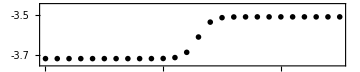

```mathematica
gmaxTh=ListPlot[MapThread[List,{TsTh,(*1/Abs@*)LambdaMaxTh}],
Frame->True,
FrameTicks->{{Range[-3.7,-3.5,0.1],None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{max}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{-3.75,-3.45}}]
```

```mathematica
Export[NotebookDirectory[]<>"10D_max_Eigenvalue_Theory.pdf",gmaxTh]
```

C:\Users\alish\Desktop\stability paper\10D_max_Eigenvalue_Theory.pdf

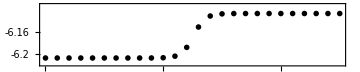

```mathematica
gminTh=ListPlot[MapThread[List,{TsTh,(*1/Abs@*)LambdaMinTh}],
Frame->True,
FrameTicks->{{Range[-6.2,-6.14,0.02],None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{min}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{-6.22,-6.11}}]
```

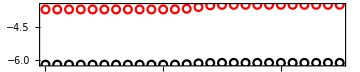

```mathematica
glambdaTheory=ListPlot[{MapThread[List,{TsTh,(*1/Abs@*)LambdaMinTh}],MapThread[List,{TsTh,(*1/Abs@*)LambdaMaxTh}]},
Frame->True,
FrameTicks->{{(*Range[-3.5,-1.5,1]*)Automatic,None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,(*{-4,-1}*)Automatic},
PlotLegends->Placed[leglambda,{0.2,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2Eigenvalue_Theory.pdf",glambdaTheory]
```

C:\Users\alish\Desktop\stability paper\2Eigenvalue_Theory.pdf

```mathematica
legtime=PointLegend[{Black,Red},{MaTeX["1/|\\lambda_{min}|",FontSize->10],MaTeX["1/|\\lambda_{max}|",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

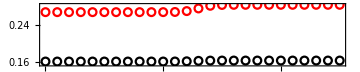

```mathematica
gtimescaleTheory=ListPlot[{MapThread[List,{TsTh,1/Abs@LambdaMinTh}],MapThread[List,{TsTh,1/Abs@LambdaMaxTh}]},
Frame->True,
FrameTicks->{{Automatic(*Range[0.3,0.7,0.2]*),None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,(*{0.2,0.8}*)Automatic},
PlotLegends->Placed[legtime,{0.25,0.5}]]
```

```mathematica
Export[NotebookDirectory[]<>"2timescale_Theory.pdf",glambdaTheory]
```

C:\Users\alish\Desktop\stability paper\2timescale_Theory.pdf

```mathematica
AllFPsNumber={1,1,1,1,1,1,1,1,1,1,1,1,1,483,782,745,745,745,745,745,745,745,745,745,745,745};
```

```mathematica
StableFPsNumber={1,1,1,1,1,1,1,1,1,1,1,1,1,11,11,11,11,11,11,11,11,11,11,11,11,11};
```

```mathematica
UnstableFPsNumber={0,0,0,0,0,0,0,0,0,0,0,0,0,472,771,734,734,734,734,734,734,734,734,734,734,734};
```

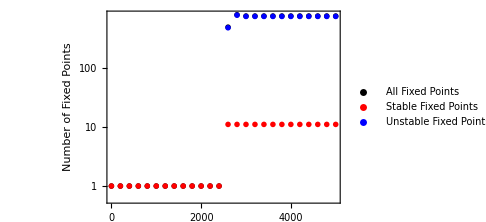

```mathematica
gFP=ListLogPlot[{MapThread[List,{TsTh,AllFPsNumber}],MapThread[List,{TsTh,StableFPsNumber}],MapThread[List,{TsTh,UnstableFPsNumber}]},
Frame->True,
FrameTicks->{{Automatic(*Range[0.3,0.7,0.2]*),None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],Style["Number of Fixed Points",12,Black,FontFamily->"Times"]},
(*AspectRatio->GoldenRatio,*)
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black,Red,Blue},
PlotRange->All(*{Automatic,{-50,850}}*),
(*ScalingFunctions->{Automatic"Log"},*)
PlotLegends->Placed[{Style["All Fixed Points",10,FontFamily->"Times"],Style["Stable Fixed Points",10,FontFamily->"Times"],Style["Unstable Fixed Points",10,FontFamily->"Times"]},{0.25,0.75}]]
```

```mathematica
Export[NotebookDirectory[]<>"FixedPoint_Numbers_Theory_5000.pdf",gFP]
```

C:\Users\alish\Desktop\stability paper\FixedPoint_Numbers_Theory_5000.pdf

## Figures for Data and Theory

```mathematica
LambdaMax={-3.70809,-3.71312,-3.7244,-3.70336,-3.65495,-3.65166,-3.63815,-3.63755,-3.63831,-3.58852,-3.56152,-3.50573,-3.51075,-3.47374,-3.45751,-3.46783,-3.45203,-3.46582,-3.46535,-3.45,-3.46}
```

{-3.70809,-3.71312,-3.7244,-3.70336,-3.65495,-3.65166,-3.63815,-3.63755,-3.63831,-3.58852,-3.56152,-3.50573,-3.51075,-3.47374,-3.45751,-3.46783,-3.45203,-3.46582,-3.46535,-3.45,-3.46}

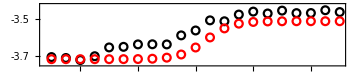

```mathematica
glambdaMaxDataTheory=ListPlot[{MapThread[List,{Ts,(*1/Abs@*)LambdaMax}],MapThread[List,{TsTh,(*1/Abs@*)LambdaMaxTh}]},
Frame->True,
FrameTicks->{{Range[-3.7,-3.5,0.1],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{max}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{-3.75,-3.42}},
PlotLegends->Placed[{Style["Data-Driven",10,FontFamily->"Times"],Style["Theory",10,FontFamily->"Times"]},{0.15,0.65}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_max_Eigenvalue_Theory_Data.pdf",glambdaMaxDataTheory]
```

C:\Users\alish\Desktop\stability paper\10D_max_Eigenvalue_Theory_Data.pdf

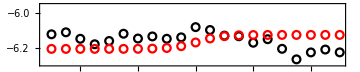

```mathematica
glambdaMinDataTheory=ListPlot[{MapThread[List,{Ts,(*1/Abs@*)LambdaMin}],MapThread[List,{TsTh,(*1/Abs@*)LambdaMinTh}]},
Frame->True,
FrameTicks->{{(*Range[-3.7,-3.5,0.1]*)Automatic,None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{min}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{-6.3,-5.95}},
PlotLegends->Placed[PointLegend[{Black,Red},{Style["Data-Driven",10,FontFamily->"Times"],Style["Theory",10,FontFamily->"Times"]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"],{0.25,0.85}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_min_Eigenvalue_Theory_Data.pdf",glambdaMinDataTheory]
```

C:\Users\alish\Desktop\stability paper\10D_min_Eigenvalue_Theory_Data.pdf

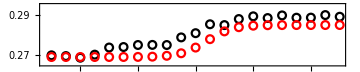

```mathematica
gTimescaleMaxDataTheory=ListPlot[{MapThread[List,{Ts,1/Abs@LambdaMax}],MapThread[List,{TsTh,1/Abs@LambdaMaxTh}]},
Frame->True,
FrameTicks->{{Range[0.27,0.29,0.01],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{max}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{0.265,0.295}},
PlotLegends->Placed[{Style["Data-Driven",10,FontFamily->"Times"],Style["Theory",10,FontFamily->"Times"]},{0.15,0.65}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_max_TimeScale_Theory_Data.pdf",gTimescaleMaxDataTheory]
```

C:\Users\alish\Desktop\stability paper\10D_max_TimeScale_Theory_Data.pdf

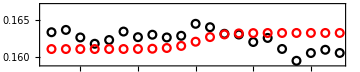

```mathematica
gTimescaleMinDataTheory=ListPlot[{MapThread[List,{Ts,1/Abs@LambdaMin}],MapThread[List,{TsTh,1/Abs@LambdaMinTh}]},
Frame->True,
FrameTicks->{{(*Range[0.27,0.29,0.01]*)Automatic,None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{min}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{0.159,0.167}},
PlotLegends->Placed[PointLegend[{Black,Red},{Style["Data-Driven",10,FontFamily->"Times"],Style["Theory",10,FontFamily->"Times"]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"],{0.25,0.85}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_min_TimeScale_Theory_Data.pdf",gTimescaleMinDataTheory]
```

C:\Users\alish\Desktop\stability paper\10D_min_TimeScale_Theory_Data.pdf

## Phase Portraits

### Data Based

#### First Window

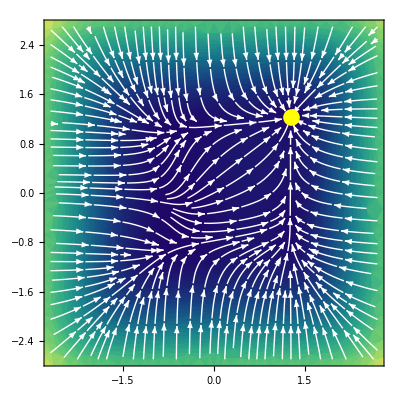

```mathematica
gfirstwin=With[{l=1},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),
StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_firstwin_500.pdf",gfirstwin]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_firstwin_500.pdf

#### Last Window

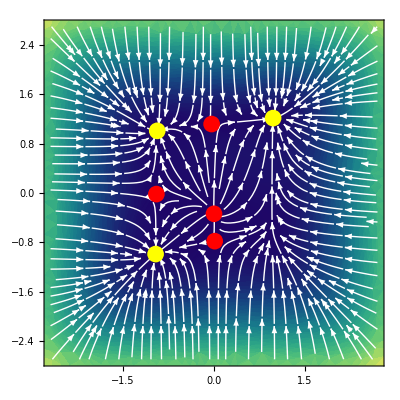

```mathematica
glastwin=With[{l=MN},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),
StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_lastwin_500.pdf",glastwin]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_lastwin_500.pdf

#### Animation

```mathematica
An=Manipulate[With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameLabel->{None,None,Style["",12],Style["",12]},StreamMarkers->"Arrow",StreamScale->0.1]],
{{l,1,Style["l",12]},1,31,1}]
```

```mathematica
Export[NotebookDirectory[]<>"Animate1.avi",An]
```

C:\Users\alish\Desktop\stability paper\Animate1.avi

### Theory